```mathematica
Clear["Global`*"]
Q = {{1-α,0,α},{0,1,0},{0,0 ,1}}; 
Q//MatrixForm
```

(1-α | 0 | α
0 | 1 | 0
0 | 0 | 1)

```mathematica
P = {{1,0,1+w},{1+w,1,0},{0,1+w,1}};
P//MatrixForm
```

(1 | 0 | 1+w
1+w | 1 | 0
0 | 1+w | 1)

```mathematica
Frequency = {x,y,z};
Fitness = P.Frequency;
ϕ = Frequency.Fitness //FullSimplify;
RHSX = x*Q[[1,1]]*Fitness[[1]] + y*Q[[2,1]]*Fitness[[2]] + z*Q[[3,1]]*Fitness[[3]]-x*ϕ;
RX = RHSX /. {z -> 1-x-y} //FullSimplify;
RHSY = x*Q[[1,2]]*Fitness[[1]] + y*Q[[2,2]]*Fitness[[2]] + z*Q[[3,2]]*Fitness[[3]]-y*ϕ;
RY = RHSY /. {z -> 1-x-y} //FullSimplify;
F = {RX,RY}
FPrules =Solve[RX==0 && RY==0,{x,y}]//FullSimplify;
FPS = {x,y}/.FPrules;
```

{x (x-x^2-x y-y^2+(-1+y) α+w (x^2+x (-2+y+α)+(-1+y) (-1+y+α))),y ((-1+w) x^2+(-1+y) (1+(-1+w) y)+x (2+(-1+w) y))}

```mathematica
Assuming[{w>0},FullSimplify[Series[FPS,{α,0,1}]]];
```

```mathematica
G = F/. {x -> u-(v/3^{1/2}),y -> 2*v/3^{1/2}};
xp = Part[G,1];
yp = Part[G,2];
vp = 3^{1/2}*yp/2;
up = xp + yp/2;
H = {up,vp}//FullSimplify;
F = H/. {u->x+1/2, v-> y+1/(2*3^(1/2))}// FullSimplify;
X = {x,y};
F = Flatten[F]
```

{1/18 (18 (-1+w) x^3-3 (1+w) (√3-3 y) y+2 (2+w) (-1+2 √3 y-3 y^2) α+9 x^2 (-1+w (-1+2 α))+3 x (1-w+6 (-1+w) y^2-4 α+2 √3 y (-1+w+2 α))),-1/18 (√3+6 y) (-3 (1+w) x-3 (-1+w) x^2+(-1+w) (√3-3 y) y)}

```mathematica
FPnew = {(2x+y-1)/2,(3y-1)/(2*3^(1/2))}/.FPrules //FullSimplify;
```

```mathematica
F/.{x->FPnew[[1]][[1]],y->FPnew[[1]][[2]]}//Simplify;
F/.{x->FPnew[[2]][[1]],y->FPnew[[2]][[2]]}//Simplify;
F/.{x->FPnew[[3]][[1]],y->FPnew[[3]][[2]]}//Simplify;
F/.{x->FPnew[[4]][[1]],y->FPnew[[4]][[2]]}//Simplify;
F/.{x->FPnew[[5]][[1]],y->FPnew[[5]][[2]]}//Simplify;
F/.{x->FPnew[[6]][[1]],y->FPnew[[6]][[2]]}//Simplify;
F/.{x->FPnew[[7]][[1]],y->FPnew[[7]][[2]]}//Simplify;
```

```mathematica
(*Given a w want to find Hopf in α*)
```

```mathematica
(*############FP1 - (0,0)###############*)
XP = Part[F,1];
YP = Part[F,2];
Jacc = D[F,{X}]/.{x->FPnew[[1]][[1]],y->FPnew[[1]][[2]]};
Jacc //FullSimplify// MatrixForm
```

(w-(1+w) α | ((1+w) (-1+α))/(√3)
0 | -1)

```mathematica
Eigenvalues[{{w-(1+w) α,((1+w) (-1+α))/(√3)},{0,-1}}]
```

{-1,w-α-w α}

```mathematica
(*Bifurcation at α=w/(1+w). α<w/(1+w)->saddle. α>w/(1+w)->Stable Node.
collides with FP7*)
```

```mathematica
(*############FP2 -near (1,0) on y==0 edge ###############*) (*Need to examine*)
XP = Part[F,1];
YP = Part[F,2];
Jacc = D[F,{X}]/.{x->FPnew[[2]][[1]],y->FPnew[[2]][[2]]};
Jacc //FullSimplify// MatrixForm
```

((1+w^2 α^2+√(1+α (-4+w (2+w α)))-2 w √(1+α (-4+w (2+w α)))+α (-4+w (2+√(1+α (-4+w (2+w α))))))/(2 (-1+w)) | (1+w^2 (-1+α)-w (-2+α) α-α (2+√(1+α (-4+w (2+w α)))))/(√3 (-1+w))
0 | (1-2 α+w^2 (2+(-2+α) α)-√(1+α (-4+w (2+w α)))+w (-2+α) √(1+α (-4+w (2+w α))))/(2 (-1+w)))

```mathematica
Tr[%94]//FullSimplify
```

```mathematica
(1-3 α+w (w+α+w (-1+α) α-2 √(1+α (-4+w (2+w α)))+α √(1+α (-4+w (2+w α)))))/(-1+w)/.√(1+α (-4+w (2+w α)))->A
```

(1-3 α+w (-2 A+w+α+A α+w (-1+α) α))/(-1+w)

```mathematica
FullSimplify[(1-3 α+w (-2 A+w+α+A α+w (-1+α) α))/(-1+w)]
```

```mathematica
(1-3 α+w (w+A (-2+α)+α+w (-1+α) α))/(-1+w)/.A->√(1+α (-4+w (2+w α)))
```

(1-3 α+w (w+α+w (-1+α) α+(-2+α) √(1+α (-4+w (2+w α)))))/(-1+w)

```mathematica
Det[%94]/.√(1+α (-4+w (2+w α)))->A//FullSimplify
```

```mathematica
1/(2 (-1+w)^2)((-α+w^2 (3+(-3+α) α)) (1+α (-4+w (2+w α)))+A (α+w (-2+w+w (-3+α) α-3 (-2+α) α+w^2 (-2+α) (1+(-1+α) α))))/.A->√(1+α (-4+w (2+w α)))
```

1/(2 (-1+w)^2)((-α+w^2 (3+(-3+α) α)) (1+α (-4+w (2+w α)))+√(1+α (-4+w (2+w α))) (α+w (-2+w+w (-3+α) α-3 (-2+α) α+w^2 (-2+α) (1+(-1+α) α))))

```mathematica
Manipulate[ParametricPlot[{{1/(2 (-1+w)^2)((-α+w^2 (3+(-3+α) α)) (1+α (-4+w (2+w α)))+√(1+α (-4+w (2+w α))) (α+w (-2+w+w (-3+α) α-3 (-2+α) α+w^2 (-2+α) (1+(-1+α) α)))),(1-3 α+w (w+α+w (-1+α) α+(-2+α) √(1+α (-4+w (2+w α)))))/(-1+w)},{α,Sqrt[4α]},{α,-Sqrt[4α]}},{α,0,1},AspectRatio->1],{w,0,2}]
```

```mathematica
FPS[[2]]
```

```mathematica
(1+w (-2+α)+√(1+α (-4+w (2+w α))))/(2-2 w)
```

(1+w (-2+α)+√(1+α (-4+w (2+w α))))/(2-2 w)

```mathematica
Plot3D[{(1+w (-2+α)+√(1+α (-4+w (2+w α))))/(2-2 w),(1+w (-2+α)-√(1+α (-4+w (2+w α))))/(2 -2w),1,0},{w,0,2},{α,0,1}]
```

-Graphics3D-

```mathematica
Solve[1+α (-4+w (2+w α))==0,α]//FullSimplify
Solve[1+w (-2+α)==0,α]
```

{{α→1/(2+2 √(1-w)-w)},{α→-1/(-2+2 √(1-w)+w)}}

{{α→(-1+2 w)/w}}

```mathematica
α/.{{α->1/(2+2 √(1-w)-w)},{α->-1/(-2+2 √(1-w)+w)}}
```

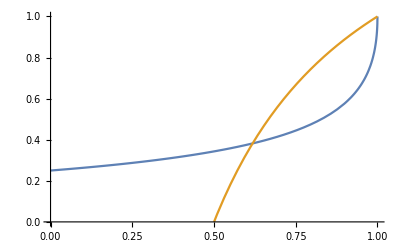

```mathematica
Plot[{1/(2+2 √(1-w)-w),(-1+2 w)/w},{w,0,1},PlotRange->{{0,1},{0,1}}]
```

```mathematica
(*############FP3- ((-1-w (-2+α)+√(1+α (-4+w (2+w α))))/(2 (-1+w)),0) *) (*Need to examine*)
XP = Part[F,1];
YP = Part[F,2];
Jacc = D[F,{X}]/.{x->FPnew[[3]][[1]],y->FPnew[[3]][[2]]};
Jacc //FullSimplify// MatrixForm
```

((1+w^2 α^2-√(1+α (-4+w (2+w α)))+2 w √(1+α (-4+w (2+w α)))-α (4+w (-2+√(1+α (-4+w (2+w α))))))/(2 (-1+w)) | (1+w^2 (-1+α)-w (-2+α) α+α (-2+√(1+α (-4+w (2+w α)))))/(√3 (-1+w))
0 | (1-2 α+w^2 (2+(-2+α) α)+√(1+α (-4+w (2+w α)))-w (-2+α) √(1+α (-4+w (2+w α))))/(2 (-1+w)))

```mathematica
Tr[%32]/.√(1+α (-4+w (2+w α)))->A//FullSimplify
```

```mathematica
(1-3 α+w (w-A (-2+α)+α+w (-1+α) α))/(-1+w)/.A->√(1+α (-4+w (2+w α)))//FullSimplify
```

(1-3 α+w (w+α+w (-1+α) α-(-2+α) √(1+α (-4+w (2+w α)))))/(-1+w)

```mathematica
Det[%32]/.√(1+α (-4+w (2+w α)))->A//FullSimplify
```

```mathematica
1/(2 (-1+w)^2)((-α+w^2 (3+(-3+α) α)) (1+α (-4+w (2+w α)))-A (α+w (-2+w+w (-3+α) α-3 (-2+α) α+w^2 (-2+α) (1+(-1+α) α))))/.A->√(1+α (-4+w (2+w α)))//FullSimplify
```

1/(2 (-1+w)^2)((-α+w^2 (3+(-3+α) α)) (1+α (-4+w (2+w α)))-√(1+α (-4+w (2+w α))) (α+w (-2+w+w (-3+α) α-3 (-2+α) α+w^2 (-2+α) (1+(-1+α) α))))

```mathematica
(*############FP4- (0,1) ###############*) (*Need to examine*)
XP = Part[F,1];
YP = Part[F,2];
Jacc = D[F,{X}]/.{x->FPnew[[3]][[1]],y->FPnew[[3]][[2]]};
Jacc //FullSimplify// MatrixForm
```

((1+w^2 α^2-√(1+α (-4+w (2+w α)))+2 w √(1+α (-4+w (2+w α)))-α (4+w (-2+√(1+α (-4+w (2+w α))))))/(2 (-1+w)) | (1+w^2 (-1+α)-w (-2+α) α+α (-2+√(1+α (-4+w (2+w α)))))/(√3 (-1+w))
0 | (1-2 α+w^2 (2+(-2+α) α)+√(1+α (-4+w (2+w α)))-w (-2+α) √(1+α (-4+w (2+w α))))/(2 (-1+w)))

```mathematica
Tr[Jacc]/.√(1+α (-4+w (2+w α)))->A//FullSimplify
```

```mathematica
((A+w)^2+α-w (1+A+w) α)/(-1+w)/.{√(1+α (-4+w (2+w α)))->A}
```

((A+w)^2+α-w (1+A+w) α)/(-1+w)

```mathematica
/.{√(1+α (-4+w (2+w α)))->A}
```

(1-3 α+w (w-A (-2+α)+α+w (-1+α) α))/(-1+w)

```mathematica
Tr[%34]//FullSimplify
```

```mathematica
(*############FP5- does not exist (except at w=0 when it is (0,1)) ###############*)
Manipulate[Plot[{(-2+w+α-√(-4 α+(w+α)^2))/(2 (-1+w)),(w-α+√(-4 α+(w+α)^2))/(2 (-1+w)),0,1},{w,0,2}],{α,0,1}]
```

```mathematica
(*############FP6- exists briefly for some small w near to (1-c1,0+c2) ###############*)(*Need to examine*)
XP = Part[F,1];
YP = Part[F,2];
Jacc = D[F,{X}]/.{x->FPnew[[6]][[1]],y->FPnew[[6]][[2]]};
Jacc =Jacc //FullSimplify;
```

```mathematica
traceFP6[α_,w_] =Tr[Jacc]//FullSimplify;
determinantFP6[α_,w_] =Det[Jacc]//FullSimplify;
```

```mathematica
Manipulate[ParametricPlot[{{determinantFP6[α,w],traceFP6[α,w]},{α,Sqrt[4α]},{α,-Sqrt[4α]}},{α,0,1},AspectRatio->1],{w,0,4}]
```

```mathematica
(*############FP7- near(1/3,1/3) ###############*)
XP = Part[F,1];
YP = Part[F,2];
Jacc = D[F,{X}]/.{x->FPnew[[7]][[1]],y->FPnew[[7]][[2]]};
Jacc =Jacc//Simplify;
traceFP7[α_,w_] =Tr[Jacc]//Simplify;
determinantFP7[α_,w_] =Det[Jacc]//Simplify;
```

```mathematica
ContourPlot[traceFP7[α,w]==0,{w,0,1},{α,0,1},PlotRange->{{0,1},{0,1/2}}]
```

```mathematica
(*######### Vector Field #########*)
Manipulate[StreamPlot[{x (x-x^2-x y-y^2+(-1+y) α+w (x^2+x (-2+y+α)+(-1+y) (-1+y+α))),y ((-1+w) x^2+(-1+y) (1+(-1+w) y)+x (2+(-1+w) y))},{x,0,1},{y,0,1},RegionFunction->Function[{x,y,vx,vy,n},x +y<1]],{α,0,.7},{w,0,.8}]
```

```mathematica
F/.{y->0}
```

{x (x-x^2+w (1+x^2+x (-2+α)-α)-α),0}

```mathematica
(*########### Bifurcation Diagram ############*)
```

```mathematica
tp7=-((-2-10 w-12 w^2-10 w^3-2 w^4+9 α+22 w α+24 w^2 α+15 w^3 α+2 w^4 α-3 α^2-12 w α^2-16 w^2 α^2-10 w^3 α^2-w^4 α^2+w α^3+3 w^2 α^3+2 w^3 α^3+4 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+4 w √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+4 w^2 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)-3 α √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)-5 w α √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)-4 w^2 α √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+w α^2 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+w^2 α^2 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2))/(2 (-1+w) (1+w+w^2) (3-3 α+α^2)));
```

```mathematica
SNCURVE =1/(2+2 √(1-w)-w) ;
```

```mathematica
HCDATAFINAL ={{0.150046826508454,0.150609551693554},{0.149454492412767,0.150751686778157},{0.148683393462556,0.15093538321942},{0.14767917778256,0.151172362173348},{0.14636753724492,0.15147807548106},{0.144657346660799,0.151870247251767},{0.142425708150328,0.152371156799959},{0.139509533239465,0.153007468950321},{0.135696052104335,0.153808912782895},{0.130702452682302,0.154806962704185},{0.124511122416913,0.155965596814164},{0.118269651095819,0.157047912160656},{0.111984000045062,0.158053557188756},{0.105626379054879,0.158987162346116},{0.0992403312022213,0.159842795333848},{0.092830698167242,0.160621189130498},{0.0863561492096548,0.161328076092867},{0.0798693298147145,0.161958677760566},{0.0733727363024902,0.162514769982948},{0.0668374187811814,0.163000454494551},{0.0602993974267339,0.16341487810599},{0.0537607428696054,0.163760435262234},{0.0471882730901528,0.164040993785876},{0.0406280563757347,0.164256977572076},{0.0340871491421383,0.164411379685667},{0.027594482666596,0.16450723687857},{0.021151036103082,0.164548604924323},{0.0191620901780185,0.164550994103252},{0.0147795819571606,0.164539613212124},{0.00851211709751864,0.164485076709615},{0.00239236449010689,0.164390719965809},{0.00324218142653292,0.16440615427438},{0.00940287091957719,0.164495487196276},{0.015721467131603,0.164543959330498},{0.0191620450564529,0.164550994103227},{0.0221418442718938,0.164545615912881},{0.0286121167106949,0.164495878271068},{0.0351307965568596,0.164390708938605},{0.041683275022121,0.164226440790076},{0.048254003962179,0.163999936681896},{0.0548401185227965,0.163708030456165},{0.061437570089126,0.16334775932529},{0.0680211597683462,0.162917853386898},{0.0746063966604985,0.162414867315429},{0.0811914336419211,0.161836339922363},{0.0877048429793602,0.161187288675068},{0.0942072759987938,0.160460689712325},{0.100695031150947,0.159655004560908},{0.107152782054333,0.15877054688887},{0.113583585413711,0.157805527186888},{0.119980807567316,0.156759595198259},{0.126248602612236,0.155649109577505},{0.13246671899295,0.15446092075868},{0.138628809712851,0.153195626174509},{0.144677851629589,0.15186558804347},{0.150658536762053,0.150461828320527},{0.156566466112882,0.14898526565325},{0.16235339446177,0.147449000285785},{0.168060973150338,0.145843163320444},{0.173687320578449,0.144168547520637},{0.179197077154177,0.142436906540713},{0.184624491583673,0.140638836561628},{0.189969541532191,0.138774973548776},{0.19523542687468,0.136844906782685},{0.200418887873564,0.134850744445676},{0.205521032624948,0.132793286962187},{0.210519980162844,0.130683478671199},{0.21543999574781,0.128513492502238},{0.220283000155082,0.126284548404894},{0.225041886688448,0.124002566093169},{0.229725683147729,0.121666278859209},{0.234336867643269,0.119277681470064},{0.238857773869115,0.116850114556807},{0.243310617227905,0.114376241934637},{0.247698291127138,0.111858891870845},{0.25205462966209,0.109282680890767},{0.256349567455501,0.106669930228562},{0.260586463039129,0.104024413981969},{0.264752977928482,0.101360369441186},{0.268867616343855,0.0986728048447242},{0.272934265563345,0.0959659597022902},{0.276945092154724,0.0932522473117467},{0.280915858746795,0.0905283427210908},{0.284850525126844,0.0877988023107385},{0.288754075147419,0.0850675115867404},{0.292625581780069,0.0823425129030443},{0.296468950961044,0.079628423849597},{0.300283113384898,0.0769332385984389},{0.304076362839992,0.0742581342116283},{0.307852473797135,0.0716072514462496},{0.311598969863521,0.0689957547104316},{0.315335242622335,0.0664161631661819},{0.319065026745733,0.0638717242872907},{0.322825370389224,0.0613431557523184},{0.326584764979676,0.0588573824271236},{0.330346526654014,0.0564170651797354},{0.334077508381904,0.0540474328353732},{0.337816604928192,0.0517270344224605},{0.341567095786455,0.0494574696867035},{0.345339408765542,0.0472359164279228},{0.349130019784612,0.0450676667198768},{0.352941954914747,0.0429537555257213},{0.356757615608719,0.0409058872913403},{0.360595904590877,0.0389154754466805},{0.36445947063222,0.0369828928268114},{0.368353596737774,0.035107089280571},{0.372273199055153,0.0332917827437981},{0.376220624184238,0.0315367364842194},{0.380215598094443,0.0298343274779241},{0.38424118062598,0.0281927431580715},{0.388299625238232,0.0266113205055508},{0.392418256890504,0.0250802336235803},{0.396569169074661,0.0236103792610065},{0.400754637825199,0.0222006006422211},{0.404995424713416,0.0208439279578181},{0.409271868882057,0.0195465112249963},{0.413585779409902,0.0183070330994091},{0.41788900808852,0.0171373363282266},{0.422228557803638,0.016022569847836},{0.426605809371818,0.0149613033674181},{0.430997675724744,0.0139575071480018},{0.435426996215622,0.0130042917068783},{0.439895069088357,0.0121001133166934},{0.444399380703474,0.0112441313285687},{0.448941222886649,0.0104346841779652},{0.453521512409135,0.00967017603871674},{0.458129743917337,0.00895073386386289},{0.462775856582577,0.00827317091703696},{0.467460475224013,0.00763589267885145},{0.472167017506809,0.00703940759902722},{0.47691150236439,0.00647997844145308},{0.481694108371754,0.00595606583228276},{0.486496751944876,0.00546787156703711},{0.491336569024702,0.00501207368879037},{0.49621238758525,0.00458723498977048},{0.501116891726868,0.0041924342636586},{0.506055299631344,0.00382570363690234},{0.511027768772338,0.00348557053700068},{0.516092800662609,0.00316716691805806},{0.521188501392102,0.00287323500764723},{0.526317909356452,0.00260224349717961},{0.53145458113214,0.00235406485551552},{0.536618259741469,0.00212618445845131},{0.541809840508069,0.00191725997866441},{0.546989410625171,0.00172741672736909},{0.552194862229722,0.00155387957385342},{0.557425484778416,0.00139552207364914},{0.562705602104315,0.00125061892955572},{0.56801037293231,0.0011189081795176},{0.573339306976582,0.000999402019095406},{0.578764652251555,0.000889770408395997},{0.584209493241322,0.000790869286095922},{0.589673749602732,0.000701800900582108},{0.595073624280671,0.000622881776518663},{0.600496838493679,0.000551880647375163},{0.605943449160166,0.000488116219818362},{0.611308373731389,0.000431992740926033},{0.616690073647205,0.00038171606962587},{0.622089176658492,0.000336746972759486},{0.627498960602928,0.000296640426959397},{0.632924000290914,0.000260897146169325},{0.638365117599647,0.000229091212067022},{0.643858658979564,0.000200658598259579},{0.649368275799112,0.000175466626706013},{0.65489446614148,0.000153181741245067},{0.660419762289698,0.000133562899664944},{0.665962318195926,0.000116258529601026},{0.671524861361381,0.000101017063436684},{0.677123572606429,0.0000875861364041279},{0.68273067682654,0.0000758234647619119},{0.688353421204193,0.0000655298475861003},{0.693955445078355,0.0000566161090538275},{0.699527003955093,0.0000488734948029217},{0.705114912306647,0.0000421188752050851},{0.710689068377144,0.0000362409852023225},{0.716351240106929,0.0000310901357983393},{0.722030990780021,0.0000266246841991868},{0.727684224203861,0.0000227911853067236},{0.733340731518776,0.0000194812398742766},{0.739014080561149,0.0000166234047399223},{0.744690013443753,0.000014162659135423},{0.750405501264045,0.0000120403340603474},{0.756138253127017,0.0000102181865620231},{0.761859887950909,8.66348565799121*^-6},{0.767600686015802,7.33236151877182*^-6},{0.773358718020259,6.19494729909037*^-6},{0.779141352160585,5.22317315422906*^-6},{0.784951044191697,4.39524122621804*^-6},{0.790778745022667,3.69195287546718*^-6},{0.796661075073701,3.09203708588533*^-6},{0.802567739332551,2.5845834725394*^-6},{0.808493325719448,2.15643806181726*^-6},{0.814641939037857,1.78440736695069*^-6},{0.820814644334523,1.47361954343729*^-6},{0.827001437451816,1.21478064953555*^-6},{0.832945023083373,1.00766567484689*^-6},{0.838913328599899,8.34243409954892*^-7},{0.844899431304996,6.89413668774949*^-7},{0.851008307499612,5.66739706919797*^-7},{0.857140411012289,4.64957390394448*^-7},{0.863291735341803,3.80710990002038*^-7},{0.869463907842153,3.110746439644*^-7},{0.875674538456667,2.5352174813522*^-7},{0.881918524299029,2.06093742261849*^-7},{0.888036843373892,1.67990854400862*^-7},{0.894178945647091,1.36620880561245*^-7},{0.900342168857479,1.10849686517598*^-7},{0.906592394459054,8.9501024538949*^-8},{0.912877134042938,7.20386802687946*^-8},{0.919186055301829,5.77963067229751*^-8},{0.925416010421069,4.63630656797577*^-8},{0.931677049896469,3.70266548294143*^-8},{0.937959351123221,2.94185530264239*^-8},{0.944349357969967,2.31432492346577*^-8},{0.950772956777366,1.80384466370661*^-8},{0.957226305774287,1.38840188013477*^-8},{0.963537729343183,1.05784534239583*^-8},{0.96987538843667,7.85978805438278*^-9},{0.976236531512516,5.61392151700656*^-9},{0.982599783149059,3.75026918852499*^-9},{0.988957713223001,2.18890832578004*^-9},{0.988996400036643,2.18018225852503*^-9},{0.99540074093175,8.4455459328297*^-10}};
```

```mathematica
(*as many as six FPS at once*)
```

```mathematica
p0 = Plot[{(√w-w+w^(3/2))/(1+√w+w^(3/2))},{w,Root"0.183"Root[-1+5 #1+2 #1^2+2 #1^3+3 #1^4+#1^5&,1]0.18336505617230006,2},PlotRange->{{0,1},{0,1/2}},AspectRatio->1,PlotStyle->{Blue}];(*center collsion with y=0 edge at x = 1/(1+√w) , transcritical*)

p1 =Plot[{((1+w+w^2) (3-2 √(2-w-w^2)))/(1+2 w)^2 ,(√w-w+w^(3/2))/(1+√w+w^(3/2))},{w,0,Root"0.183"Root[-1+5 #1+2 #1^2+2 #1^3+3 #1^4+#1^5&,1]0.18336505617230006},PlotRange->{{0,1},{0,1/2}},AspectRatio->1,PlotStyle->{Red,Blue}];(*saddle-node at interior FPs / point second internal FP emerges from y=0 axis in transcritical*)

p2 = Plot[1/(2-w+2 √(1-w)) ,{w,0,1/2 (-1+√5)},PlotRange->{{0,1},{0,1/2}},AspectRatio->1,PlotStyle->{Red}];(*Collision between FPs on y==0 edge*)

p3=Plot[w/(1+w),{w,0,1},PlotRange->{{0,1},{0,1/2}},AspectRatio->1,PlotStyle->{Blue}];(*FP emerges from 0,0 along y=0 axis*)

p4 = ListLinePlot[HCDATAFINAL,PlotStyle->{Orange}];
(*Homoclinc*)

p5 =ContourPlot[tp7==0,{w,0,1},{α,0,1},PlotRange->{{0,1},{0,1/2}},AspectRatio->1,ContourStyle->{Green}];(*Hopf*)
```

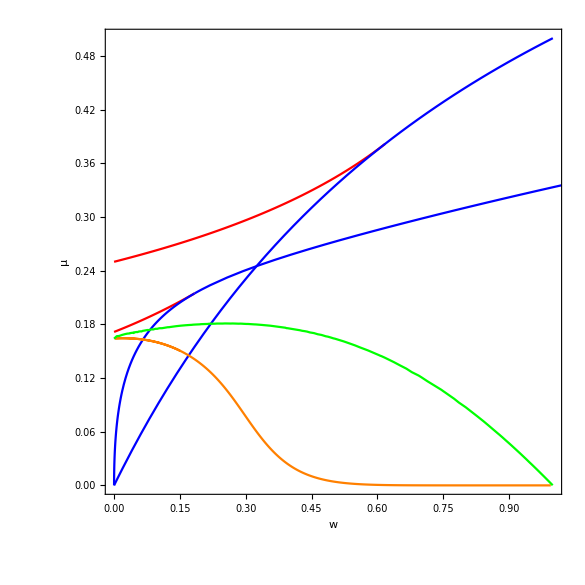

```mathematica
Show[p0,p1,p2,p3,p4,p5,Frame->True,FrameLabel->{w,μ},LabelStyle->Directive[Black,Large]]
```